# Theta-Smearing-Profile

Um zu visualisieren, wie wir die Heaviside-Θ-Funktion verschmieren.

### Vorbereitendes für den Plot

```mathematica
(* Prepare Export and metric units *)
SetDirectory[NotebookDirectory[]];
cm=72/2.54;
(* Labels direkt auf Funktionen anzeigen *)
(* Epic Epilog-Labels coming here, modified for the current problem:
   Featuring scaling and correct Inset (no rectangle nonrotated box).
 ASSUMING data be a list of X as variable, ideal for g00s. *)
ClearAll[EpiLabels]
EpiLabels[xpoint_, data_, labels_,axisratio_:1]:= 
With[{xpoints=If[Head@xpoint===List, xpoint, xpoint&/@ labels]}, (* erlaube Liste von xpoints *)
Inset[Rotate[Text[labels[[#]],Background -> White],
ArcTan@Re@N[(D[data⟦#⟧,X]/.{X-> xpoints⟦#⟧}) ] / axisratio] ,
{xpoints⟦#⟧, 0 +( data/.X-> xpoints⟦#⟧)⟦#⟧}
]& /@ Range@Length@data] (* 1: any value to introspect list*)
RootToSol[root_] := root/. {{_ -> y_}-> y} (* Extrahieren von FindRoot-Ergebnissen *)
```

## Holografie

```mathematica
h[r_]=r^(2+n)/(r^(2+n)+L^(2+n))
```

r^(2+n)/(L^(2+n)+r^(2+n))

```mathematica
ns = {0,2,7};
nsLabels = "n="<>ToString@#&/@ ns
nsColors = {Red, Blue, Darker@Green};
hGraphs[r_] = Table[h[r]/.{n->nn, L-> 1}, {n,ns}]
```

{n=0,n=2,n=7}

{r^2/(1+r^2),r^4/(1+r^4),r^9/(1+r^9)}

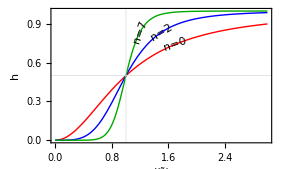

```mathematica
fig=Plot[
Evaluate@hGraphs@r,{r,0,3},
PlotRange-> {0,1},
PlotStyle-> nsColors,
GridLines-> {{1},{0.5}},
Frame-> True,
FrameLabel-> {"r/(r̃)_0", "h"},
Epilog-> {
EpiLabels[{1.7,1.5,1.2}, hGraphs[X], nsLabels, 0.65]
},
ImageSize -> 10cm,
PlotRangePadding->None,
AspectRatio-> 0.60
]
```

```mathematica
Export["../figures/profile-h.pdf", Show@fig]
```

../figures/profile-h.pdf

### Holographie-Dirac (Ableitung)

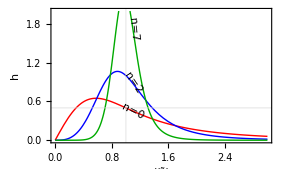

```mathematica
dhGraphs[r_]=D[hGraphs@r,r];
fig=Plot[
Evaluate@dhGraphs@r,{r,0,3},
PlotRange-> {0,2},
PlotStyle-> nsColors,
GridLines-> {{1},{0.5}},
Frame-> True,
FrameLabel-> {"r/(r̃)_0", "h"},
Epilog-> {
EpiLabels[{1.1,1.1,1.1}, dhGraphs[X], nsLabels, 3/2 * 0.65]
},
ImageSize -> 10cm,
PlotRangePadding->None,
AspectRatio-> 0.60
]
```

```mathematica
Export["../figures/dirac-profile-h.pdf", Show@fig]
```

../figures/dirac-profile-h.pdf

## SelF-Regular

In dem Worksheet wird Self-Encoding und Self-Regular synonym verwendet, gemeint ist immer das self-regular-Modell.

```mathematica
halpha[r_]  =r^(3+n)/((r^a+L^a/2)^((3+n)/a))
halphainf[r_] = Piecewise@{
{r^(3+n), r≤ L},
{1, r>L }}
a0[n_] = (3+n)/Log[2+n] Log[(3+n)/2];
L0[n_,a_] = (1/(1+n))^(1/a)
```

r^(3+n) (L^a/2+r^a)^(-(3+n)/a)

Piecewise[{{r^(3+n), r≤L}, {1, r>L}, {0, True}}]

(1/(1+n))^(1/a)

### Self-Regular für feste α bei verschiedenen n

```mathematica
αα = 2
ns = {0,2,7};
nsLabels = "n="<>ToString@#&/@ ns
nsColors = {Red, Blue, Darker@Green};
hαGraphs[r_] = Table[halpha[r]/.{n->nn, L-> 1, a->αα}, {n,ns}]
```

2

{n=0,n=2,n=7}

{r^3/((1/2+r^2)^(3/2)),r^5/((1/2+r^2)^(5/2)),r^10/((1/2+r^2)^5)}

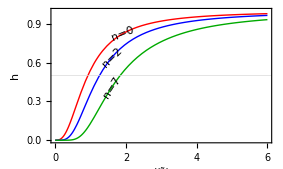

```mathematica
fig=Plot[
Evaluate@hαGraphs@r,{r,0,6},
PlotRange-> {0,1},
PlotStyle-> nsColors,
GridLines-> {{},{0.5}},
Frame-> True,
FrameLabel-> {"r/(r̃)_0", "h"},
Epilog-> {
EpiLabels[{1.9,1.6,1.6}, hαGraphs[X], nsLabels, 0.4]
},
ImageSize -> 10cm,
PlotRangePadding->None,
AspectRatio-> 0.60
]
```

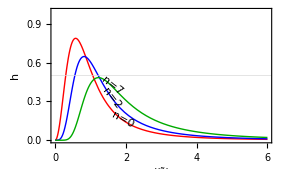

```mathematica
dhαGraphs[r_] = D[hαGraphs[r],r];
fig=Plot[
Evaluate@dhαGraphs@r,{r,0,6},
PlotRange-> {0,1},
PlotStyle-> nsColors,
GridLines-> {{},{0.5}},
Frame-> True,
FrameLabel-> {"r/(r̃)_0", "h"},
Epilog-> {
EpiLabels[{1.9,1.6,1.6}, dhαGraphs[X], nsLabels, 0.4]
},
ImageSize -> 10cm,
PlotRangePadding->None,
AspectRatio-> 0.60
]
```

### Self-encoding hα, einfach, für verschiedene α bei fixem n

Dieser Plot wird nicht verwendet, er zeigt dass es quasi unbrauchbar ist, mit der Hand verschiedene α auszuwählen.

```mathematica
nn = 2;
aa = {0.5,1,∞};
aaa = aa * a0[nn];
asLabels =  {"α=0.5 α_0", "α=α_0", "α=∞"};
nsColors = {Red, Blue, Darker@Green};
haGraphs[r_] = Join[
Table[halpha[r]/. L-> 1(*1/L0[nn,a]*), {a,Drop[aaa,-1]}],
{halphainf[r] /. L-> 1}
]/.{n->nn}
```

{r^5/((0.5+r^1.65241)^3.02588),r^5 (1/2+r^((5 Log[5/2])/Log[4]))^(-Log[4]/Log[5/2]),Piecewise[{{r^5, r≤1}, {1, r>1}, {0, True}}]}

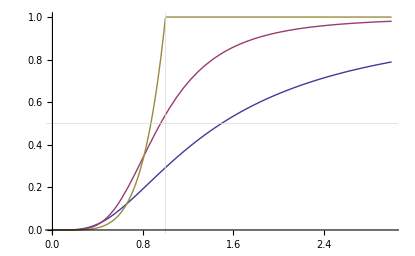

```mathematica
Plot[
Evaluate@haGraphs[r ],{r,0,3},
GridLines-> {{1},{0.5}},
PlotRange-> {0,1}]
```

Beobachtung: α_0 hat tatsächlich für die Verteilung selbst keinen “besonderen” Wert, sondern nur später in Verbindung mit der Metrik (self-encoding).

### Self-encoding hα für eine äquidistante Kurvenschar, für versch. α bei fixem n

Dies basiert auf dem “Master-Thesis/remnant-plot.nb”.

```mathematica
(* halpha an der Stelle r=L ausgewertet *)
funkA[α_]=halpha[1]/. L-> 1
(* Inverse Funktion, mit der Hand berechnet, 
  da InverseFunction nicht so ueberzeugend ist: *)
InverseFunction[(3/2)^(-(3+n)/#)&]
funkAinv[f_] = -(3+n)/Log[f] Log[3/2]
```

(3/2)^(-(3+n)/a)

ConditionalExpression[(3+n)/((2 ⅈ π C[1])/Log[3/2]+Log[1/#1]/Log[3/2]),C[1]∈Integers]&

((-3-n) Log[3/2])/Log[f]

```mathematica
numAlphas = 15;
touchedHvalues = Range[0.02,1-0.02, 1/numAlphas]
ClearAll[touchedAlphas]
touchedAlphas[n_] = funkAinv/@touchedHvalues
colorScale = Lighter[Red, 0.6*Rescale[#,{0,Length@touchedAlphas@nn}]]&/@Reverse@Range@Length@touchedAlphas@nn
```

{0.02,0.0866667,0.153333,0.22,0.286667,0.353333,0.42,0.486667,0.553333,0.62,0.686667,0.753333,0.82,0.886667,0.953333}

{-0.103646 (-3-n),-0.165788 (-3-n),-0.216232 (-3-n),-0.267788 (-3-n),-0.324519 (-3-n),-0.389742 (-3-n),-0.467395 (-3-n),-0.563008 (-3-n),-0.685145 (-3-n),-0.84819 (-3-n),-1.07863 (-3-n),-1.43149 (-3-n),-2.04315 (-3-n),-3.37084 (-3-n),-8.48419 (-3-n)}

{RGBColor[1.,0.6,0.6],RGBColor[1.,0.56,0.56],RGBColor[1.,0.52,0.52],RGBColor[1.,0.48,0.48],RGBColor[1.,0.44,0.44],RGBColor[1.,0.4,0.4],RGBColor[1.,0.36,0.36],RGBColor[1.,0.32,0.32],RGBColor[1.,0.28,0.28],RGBColor[1.,0.24,0.24],RGBColor[1.,0.2,0.2],RGBColor[1.,0.16,0.16],RGBColor[1.,0.12,0.12],RGBColor[1.,0.08,0.08],RGBColor[1.,0.04,0.04]}

{{0.518229,0.0956352},{0.828939,0.230521},{1.08116,0.324625},{1.33894,0.403138},{1.62259,0.472527},{1.94871,0.535687},{2.33697,0.594223},{2.81504,0.649141},{3.42572,0.70112},{4.24095,0.750646},{5.39317,0.798082},{7.15744,0.843708},{10.2158,0.887745},{16.8542,0.930371},{42.421,0.971733}}

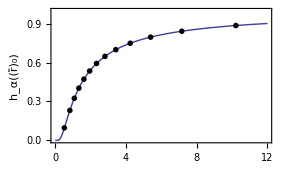

../figures/dirac-profile-halpha-alpha-choices.pdf

```mathematica
Module[{nn=0,
values=Table[{a,funkA[a]/. n-> 0},{a,touchedAlphas[nn]}]},
Print[N@values];
plot=Show[
Plot[funkA[a]/. n-> nn,{a,0,12},PlotRange-> {0,1},
Frame-> True,
ImageSize -> 10cm,
AspectRatio-> 0.6,
PlotRangePadding->None,
FrameLabel->{"α", "h_α((r̃)_0)"}],
(* "selbstgemachter" ListPlot mit Punktabhaengigen circlen (Farbe wie im Plot unten *)
Graphics@Map[Inset[Graphics@{#⟦1⟧,Disk[], Darker[#⟦1⟧,.5], Circle[]},#⟦2⟧, Center,0.35]&,Transpose@{colorScale,values}]
(* ersetzt den hier: *)
(*ListPlot[values, PlotMarkers->Graphics[{Black,Circle[]},ImageSize->8]] *)
];
Print@plot;
Export["../figures/dirac-profile-halpha-alpha-choices.pdf", plot]
]
```

{r^5/((0.5+r^0.518229)^9.64824),r^5/((0.5+r^0.828939)^6.0318),r^5/((0.5+r^1.08116)^4.62467),r^5/((0.5+r^1.33894)^3.7343),r^5/((0.5+r^1.62259)^3.08149),r^5/((0.5+r^1.94871)^2.5658),r^5/((0.5+r^2.33697)^2.13952),r^5/((0.5+r^2.81504)^1.77617),r^5/((0.5+r^3.42572)^1.45955),r^5/((0.5+r^4.24095)^1.17898),r^5/((0.5+r^5.39317)^0.927099),r^5/((0.5+r^7.15744)^0.698574),r^5/((0.5+r^10.2158)^0.48944),r^5/((0.5+r^16.8542)^0.296662),r^5/((0.5+r^42.421)^0.117866),Piecewise[{{r^5, r≤1}, {1, r>1}, {0, True}}]}

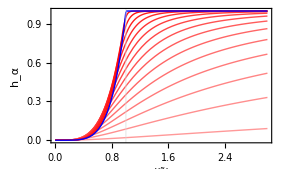

```mathematica
haEqualGraphs[r_] = Join[
Table[halpha[r]/. L-> 1, {a,touchedAlphas[nn]}],
{halphainf[r] /. L-> 1}
]/.{n->nn}
fig=Plot[
Evaluate@haEqualGraphs[r ],{r,0,3},
GridLines-> {{1},{}},
PlotRange-> {0,1},
PlotStyle-> Join[colorScale,{{Thick,Blue}}],
Frame-> True,
ImageSize -> 10cm,
PlotRangePadding->None,
AspectRatio->  0.60,
FrameLabel-> {"r/(r̃)_0", "h_α"}
]
```

```mathematica
Export["../figures/profile-halpha.pdf", Show@fig]
```

../figures/profile-halpha.pdf

### Self-Encoding-Dirac (Ableitung)

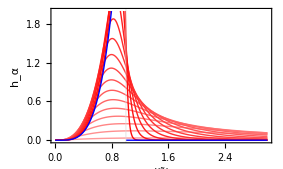

```mathematica
dhaEqualGraphs[r_] = D[haEqualGraphs@r,r];
fig=Plot[
Evaluate@dhaEqualGraphs@r,{r,0,3},
GridLines-> {{1},{}},
PlotRange-> {0,2},
PlotStyle-> Join[
Lighter[Red, 0.6*Rescale[#,{0,Length@touchedAlphas@nn}]]&/@Reverse@Range@Length@touchedAlphas@nn,
{{Thick,Blue}}
],
Frame-> True,
ImageSize -> 10cm,
PlotRangePadding->None,
PlotRangeClipping->False,
AspectRatio->  0.60,
FrameLabel-> {"r/(r̃)_0", "h_α"}
]
```

```mathematica
Export["../figures/dirac-profile-halpha.pdf", Show@fig]
```

../figures/dirac-profile-halpha.pdf